```mathematica
(*Function is adaptation of this approach: https://www.comsol.com/blogs/how-to-generate-random-surfaces-in-comsol-multiphysics *)
```

```mathematica
GaussianNoiseMatrix[n_,mean_,stddev_,seed_]:=Module[{matrix},RandomSeed[seed];
matrix=RandomVariate[NormalDistribution[mean,stddev],{n,n}];
Return[matrix]];
UniformNoiseMatrix[n_,min_,max_,seed_]:=Module[{matrix},RandomSeed[seed];
matrix=RandomVariate[UniformDistribution[{min,max}],{n,n}];
Return[matrix]];

CreateRandomSurface[gridSize_,spectralExponent_,desiredRoughness_,desiredStdDev_,noiseMean_,noiseStdDev_,uniformMin_,uniformMax_,seed_]:=Module[{coefficients,surface,scalingFactor,stdDevSurface,g,h},

g=GaussianNoiseMatrix[2 gridSize+1,noiseMean,noiseStdDev,seed];
h=UniformNoiseMatrix[2 gridSize+1,uniformMin,uniformMax,seed];

coefficients=Table[Module[{m2n2},m2n2=m^2+n^2;
If[m2n2==0,0,(m2n2)^(-spectralExponent/4)]*Exp[2 Pi I RandomReal[]] g[[m+gridSize+1,n+gridSize+1]]*Exp[2 Pi I h[[m+gridSize+1,n+gridSize+1]]]],{m,-gridSize,gridSize},{n,-gridSize,gridSize}];
coefficients=Replace[coefficients,c_/;Abs[c]<10^-10:>RandomReal[{-1,1}]+I RandomReal[{-1,1}],{2}];
Quiet[surface=InverseFourier[coefficients,FourierParameters->{1,-1}],InverseFourier::fftl];
stdDevSurface=Quiet[StandardDeviation[Flatten[Abs[surface]]]];
If[stdDevSurface>0,scalingFactor=desiredStdDev/stdDevSurface;
surface=Abs[surface]*scalingFactor;];
Return[Abs[surface]];];
```

```mathematica
surface=CreateRandomSurface[64,3,16,0.1,0.0,1,1,0.1,11542];
ListPlot3D[surface,ColorFunction->"AlpineColors",Mesh->None]
```

{-Graphics-,-Graphics-}

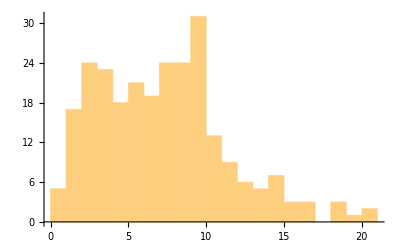
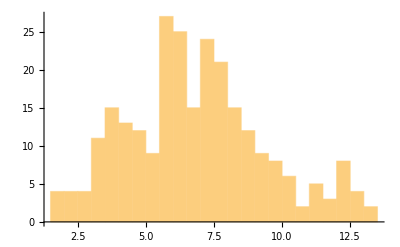

7.23799 | 7.08885 | 4.15628 | 17.2746 | 0.707913
6.84441 | 6.60437 | 2.56871 | 6.59826 | 0.385345

```mathematica
ClearAll[paramsList,results,a,statistics]
paramsList=Table[{128,n,10,4,0.0,5,0,1,12},{n,2.5,3.5,1}];
results=Table[{params,CreateRandomSurface@@params},{params,paramsList}];
ListDensityPlot[#[[2]],MeshFunctions->{#3&},Mesh->4,ColorFunction->"Rainbow",PlotLegends->Automatic]&/@results
a=results[[All,All,2]];
Histogram[#//Flatten,25,PlotRange->{All,All}]&/@a
statistics={Mean[#//Flatten],Median[#//Flatten],StandardDeviation[#//Flatten],Variance[#//Flatten],Skewness[#//Flatten]}&/@a;
statistics//TableForm
```